# Citation Network Analysis: Investigation into Endnote Bibliographic Data

## Wang Chengjun

## 20110507@HALL 8

http : // mathgis.blogspot.com/2010/04/play - with - bibliographic - data.html

## Data Clean

### Imort xml data

```mathematica
xml=Import["D:/Jonathan's COM8005/IMC/agenda-setting.xml"]
(*note: in this way, you can add your annotation*)
```

XMLObject[Document][{XMLObject[Declaration][Version→1.0,Encoding→UTF-8]},XMLElement[xml,{},{XMLElement[records,{},{XMLElement[record,{},{XMLElement[database,{name→agenda-setting.enl,path→D:\Jonathan's COM8005\IMC\agenda-setting.enl},{agenda-setting.enl}],XMLElement[source-app,{name→EndNote,version→11.0},{EndNote}],XMLElement[rec-number,{},{323}],XMLElement[foreign-keys,{},{XMLElement[key,{app→EN,db-id→pz2fewdfqdezpaexr2kx9vtxddtt22sd2005},{323}]}],XMLElement[ref-type,{name→Journal Article},{17}],XMLElement[contributors,{},{}],XMLElement[titles,{},{XMLElement[title,{},{XMLElement[style,{face→normal,font→default,size→100%},{Setting the agenda}]}],XMLElement[secondary-title,{},{XMLElement[style,{face→normal,font→default,size→100%},{Materials World}]}],XMLElement[alt-title,{},{XMLElement[style,{face→normal,font→default,size→100%},{Mater. World}]}]}],XMLElement[periodical,{},{XMLElement[full-title,{},{XMLElement[style,{face→normal,font→default,size→100%},{Materials World}]}],XMLElement[abbr-1,{},{XMLElement[style,{face→normal,font→default,size→100%},{Mater. World}]}]}],XMLElement[alt-periodical,{},{XMLElement[full-title,{},{XMLElement[style,{face→normal,font→default,size→100%},{Materials World}]}],XMLElement[abbr-1,{},{XMLElement[style,{face→normal,font→default,size→100%},{Mater. World}]}]}],XMLElement[pages,{},{XMLElement[style,{face→normal,font→default,size→100%},{34-35}]}],XMLElement[volume,{},{XMLElement[style,{face→normal,font→default,size→100%},{17}]}],XMLElement[number,{},{XMLElement[style,{face→normal,font→default,size→100%},{5}]}],XMLElement[dates,{},{XMLElement[year,{},{XMLElement[style,{face→normal,font→default,size→100%},{2009}]}],XMLElement[pub-dates,{},{XMLElement[date,{},{XMLElement[style,{face→normal,font→default,size→100%},{May}]}]}]}],XMLElement[isbn,{},{XMLElement[style,{face→normal,font→default,size→100%},{0967-8638}]}],XMLElement[accession-num,{},{XMLElement[style,{face→normal,font→default,size→100%},{ISI:000265812900024}]}],XMLElement[notes,{},{XMLElement[style,{face→normal,font→default,size→100%},{ISI Document Delivery No.: 442AU Times Cited: 0 Cited Reference Count: 0}]}],XMLElement[work-type,{},{XMLElement[style,{face→normal,font→default,size→100%},{Article}]}],XMLElement[urls,{},{XMLElement[related-urls,{},{XMLElement[url,{},{XMLElement[style,{face→normal,font→default,size→100%},{<Go to ISI>://000265812900024}]}]}]}],XMLElement[language,{},{XMLElement[style,{face→normal,font→default,size→100%},{English}]}]}],«498»,XMLElement[record,{},{XMLElement[database,{name→agenda-setting.enl,path→D:\Jonathan's COM8005\IMC\agenda-setting.enl},{agenda-setting.enl}],XMLElement[source-app,{name→EndNote,version→11.0},{EndNote}],XMLElement[rec-number,{},{443}],XMLElement[foreign-keys,{},{XMLElement[key,{app→EN,db-id→pz2fewdfqdezpaexr2kx9vtxddtt22sd2005},{443}]}],XMLElement[ref-type,{name→Journal Article},{17}],XMLElement[contributors,{},{XMLElement[authors,{},{XMLElement[author,{},{XMLElement[style,{face→normal,font→default,size→100%},{Zorn, T. E.}]}],XMLElement[author,{},{XMLElement[style,{face→normal,font→default,size→100%},{Townsley, N.}]}]}]}],XMLElement[auth-address,{},{XMLElement[style,{face→normal,font→default,size→100%},{[Townsley, Nikki] Univ Colorado, Dept Commun, Boulder, CO 80309 USA.}]}],XMLElement[titles,{},{XMLElement[title,{},{XMLElement[style,{face→normal,font→default,size→100%},{Introduction to the forum on meaning/ful work studies in organizational communication - Setting an agenda}]}],XMLElement[secondary-title,{},{XMLElement[style,{face→normal,font→default,size→100%},{Management Communication Quarterly}]}],XMLElement[alt-title,{},{XMLElement[style,{face→normal,font→default,size→100%},{Manag. Commun. Q.}]}]}],XMLElement[periodical,{},{XMLElement[full-title,{},{XMLElement[style,{face→normal,font→default,size→100%},{Management Communication Quarterly}]}],XMLElement[abbr-1,{},{XMLElement[style,{face→normal,font→default,size→100%},{Manag. Commun. Q.}]}]}],XMLElement[alt-periodical,{},{XMLElement[full-title,{},{XMLElement[style,{face→normal,font→default,size→100%},{Management Communication Quarterly}]}],XMLElement[abbr-1,{},{XMLElement[style,{face→normal,font→default,size→100%},{Manag. Commun. Q.}]}]}],XMLElement[pages,{},{XMLElement[style,{face→normal,font→default,size→100%},{147-151}]}],XMLElement[volume,{},{XMLElement[style,{face→normal,font→default,size→100%},{22}]}],XMLElement[number,{},{XMLElement[style,{face→normal,font→default,size→100%},{1}]}],XMLElement[dates,{},{XMLElement[year,{},{XMLElement[style,{face→normal,font→default,size→100%},{2008}]}],XMLElement[pub-dates,{},{XMLElement[date,{},{XMLElement[style,{face→normal,font→default,size→100%},{Aug}]}]}]}],XMLElement[isbn,{},{XMLElement[style,{face→normal,font→default,size→100%},{0893-3189}]}],XMLElement[accession-num,{},{XMLElement[style,{face→normal,font→default,size→100%},{ISI:000257779500007}]}],XMLElement[notes,{},{XMLElement[style,{face→normal,font→default,size→100%},{ISI Document Delivery No.: 328EB Times Cited: 0 Cited Reference Count: 10 Cited References: BROADFOOT KJ, 2008, MANAGE COMMUN Q, V22, P152, DOI 10.1177/0893318908318267 CHENEY G, 2008, COMMUNICATION YB, V32, P137 CHENEY G, 2008, MANAGE COMMUN Q, V22, P181, DOI 10.1177/0893318908318261 EHRENREICH B, 2002, GLOBAL WOMAN NANNIES FAIRCLOUGH N, 1995, CRITICAL DISCOURSE A JABLIN F, 2001, NEW HDB ORG COMMUNIC KUHN T, 2008, MANAGE COMMUN Q, V22, P162, DOI 10.1177/0893318908318262 LAIR DJ, 2008, MANAGE COMMUN Q, V22, P172, DOI 10.1177/0893318908318263 MUIRHEAD R, 2004, JUST WORK SASSEN S, 1996, LOSING CONTROL SOVER Zorn, Theodore E. Townsley, Nikki}]}],XMLElement[work-type,{},{XMLElement[style,{face→normal,font→default,size→100%},{Editorial Material}]}],XMLElement[urls,{},{XMLElement[related-urls,{},{XMLElement[url,{},{XMLElement[style,{face→normal,font→default,size→100%},{<Go to ISI>://000257779500007}]}]}]}],XMLElement[electronic-resource-num,{},{XMLElement[style,{face→normal,font→default,size→100%},{10.1177/0893318908318268}]}],XMLElement[language,{},{XMLElement[style,{face→normal,font→default,size→100%},{English}]}]}]}]}],{}]

### Get authors information

```mathematica
authors=Cases[xml,XMLElement["authors",_,authors_]->authors,XMLElement["notes",_,{XMLElement["style",_,name_]}]->name,Infinity];
```

```mathematica
authors=Cases[xml,XMLElement["authors",_,authors_]->authors,XMLElement["notes",_,{XMLElement["style",_,{ref_}]}]->ref,2];
```

Rule::rhs: Pattern authors_ appears on the right-hand side of rule XMLElement[.

Cases::level: Level specification XMLElement[ is not of the form n, {n}, or {m, n}.

General::stop: Further output of Cases will be suppressed during this calculation.

```mathematica
names=Cases[#,XMLElement["author",_,{XMLElement["style",_,name_]}]->name]&/@authors;
(*in this case, no need to flatten so i fix the flatten level as 0*)
```

```mathematica
Length[names]
```

6848

### Caculate the distribution

```mathematica
table=Sort[Tally[Length[#]&/@names],#1[[1]]<#2[[1]]&]
```

{{1,2668},{2,2216},{3,1498},{4,357},{5,74},{6,25},{7,3},{8,3},{9,2},{10,1},{14,1}}

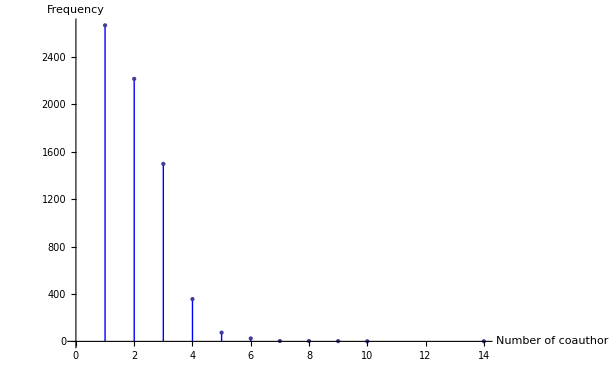

```mathematica
ListPlot[table,Filling->Axis,FillingStyle->Blue,AxesLabel->{"Number of coauthor","Frequency"}]
```

### Split the coauthors

```mathematica
split=SplitBy[#,".,"]&/@Sort[names];
```

### Permutations of co-author

```mathematica
Permutations[#,{2}]&/@split;(*however, if the length is smaller than 2, it will be blank*)
```

### GraphPlot

```mathematica
Length[Flatten[Flatten[Permutations[#,{2}]&/@split,1]/.{x_,y_}:>{x->y}]]
```

20644

```mathematica
GraphPlot[Flatten[Flatten[Permutations[#,{2}]&/@split,1]/.{x_,y_}:>{x->y}]]
```

-Graphics-